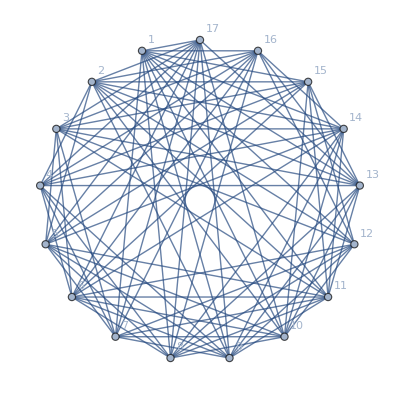

```mathematica
g=Graph[plantri[[8]]];gc=GraphComplement[g,GraphLayout->"CircularEmbedding",VertexLabels->"Name"]
```

```mathematica
gc
```

-Graphics-

```mathematica
VertexCount[gc]
```

17

```mathematica
GraphQ [gc]
```

```mathematica
ChromaticPolynomial[g,x]//CompleteBaseCoeff//Total
```

238105243

```mathematica
ChromaticPolynomial[g,17]//FactorInteger
```

{{2,5},{3,2},{5,1},{7,2},{17,2},{59,1},{401,1},{99608657,1}}

```mathematica
ChromaticPolynomial[gc,x]
```

ChromaticPolynomial[-Graphics-,x]

```mathematica
gf=FindFullFormula[g];
```

$Aborted

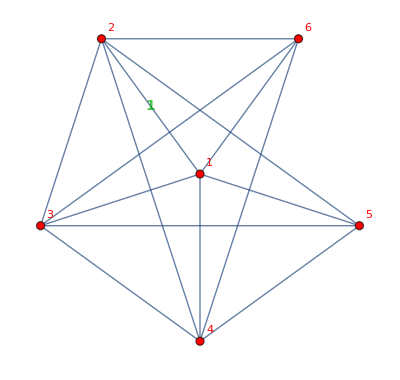

```mathematica
BarelyNColorableGraphsOfCount[6,5]
```

```mathematica
Table[IntegerPartitions[n,{4}]//Length,{n,202}]
```

{0,0,0,1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575,1650,1735,1815,1906,1991,2087,2178,2280,2376,2484,2586,2700,2808,2928,3042,3169,3289,3422,3549,3689,3822,3969,4109,4263,4410,4571,4725,4894,5055,5231,5400,5584,5760,5952,6136,6336,6528,6736,6936,7153,7361,7586,7803,8037,8262,8505,8739,8991,9234,9495,9747,10018,10279,10559,10830,11120,11400,11700,11990,12300,12600,12920,13230,13561,13881,14222,14553,14905,15246,15609,15961,16335,16698,17083,17457,17854,18239,18647,19044,19464,19872,20304,20724,21168,21600,22056,22500,22969,23425,23906,24375,24869,25350,25857,26351,26871,27378,27911,28431,28978,29511,30071,30618,31192,31752,32340,32914,33516,34104,34720,35322,35953,36569,37214,37845,38505,39150,39825,40485,41175,41850,42555,43245,43966,44671,45407,46128,46880,47616,48384,49136,49920,50688,51488,52272,53089,53889,54722,55539,56389,57222,58089}

```mathematica
LinearRecurrence[{1,1,0,0,-2,0,0,1,1,-1},{1,1,2,3,5,6,9,11,15,18},200]
```

{1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575,1650,1735,1815,1906,1991,2087,2178,2280,2376,2484,2586,2700,2808,2928,3042,3169,3289,3422,3549,3689,3822,3969,4109,4263,4410,4571,4725,4894,5055,5231,5400,5584,5760,5952,6136,6336,6528,6736,6936,7153,7361,7586,7803,8037,8262,8505,8739,8991,9234,9495,9747,10018,10279,10559,10830,11120,11400,11700,11990,12300,12600,12920,13230,13561,13881,14222,14553,14905,15246,15609,15961,16335,16698,17083,17457,17854,18239,18647,19044,19464,19872,20304,20724,21168,21600,22056,22500,22969,23425,23906,24375,24869,25350,25857,26351,26871,27378,27911,28431,28978,29511,30071,30618,31192,31752,32340,32914,33516,34104,34720,35322,35953,36569,37214,37845,38505,39150,39825,40485,41175,41850,42555,43245,43966,44671,45407,46128,46880,47616,48384,49136,49920,50688,51488,52272,53089,53889,54722,55539,56389,57222,58089,58939}

```mathematica
Table[IntegerPartitions[n,{3}]//Length,{n,50}]
```

{0,0,1,1,2,3,4,5,7,8,10,12,14,16,19,21,24,27,30,33,37,40,44,48,52,56,61,65,70,75,80,85,91,96,102,108,114,120,127,133,140,147,154,161,169,176,184,192,200,208}

```mathematica
a[n_]:=Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}];Table[a[n],{n,0,55}]
```

{1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495}

```mathematica
TraditionalForm[Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}]]
```

$Aborted

```mathematica
Table[Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}],{n,200}]
```

{1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575,1650,1735,1815,1906,1991,2087,2178,2280,2376,2484,2586,2700,2808,2928,3042,3169,3289,3422,3549,3689,3822,3969,4109,4263,4410,4571,4725,4894,5055,5231,5400,5584,5760,5952,6136,6336,6528,6736,6936,7153,7361,7586,7803,8037,8262,8505,8739,8991,9234,9495,9747,10018,10279,10559,10830,11120,11400,11700,11990,12300,12600,12920,13230,13561,13881,14222,14553,14905,15246,15609,15961,16335,16698,17083,17457,17854,18239,18647,19044,19464,19872,20304,20724,21168,21600,22056,22500,22969,23425,23906,24375,24869,25350,25857,26351,26871,27378,27911,28431,28978,29511,30071,30618,31192,31752,32340,32914,33516,34104,34720,35322,35953,36569,37214,37845,38505,39150,39825,40485,41175,41850,42555,43245,43966,44671,45407,46128,46880,47616,48384,49136,49920,50688,51488,52272,53089,53889,54722,55539,56389,57222,58089,58939,59823}

```mathematica
StandardForm[Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}]]
```

$Aborted

```mathematica
Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}]//TraditionalForm
```

$Aborted

```mathematica
Sum[i,{i,1,n}]//StandardForm
```

1/2 n (1+n)

```mathematica
Sum[Floor[(n-j-3*k+2)/2],{j,0,Floor[n/4]},{k,j,Floor[(n-j)/3]}]//TraditionalForm
```

```mathematica
CoefficientList[Series[1/((1-x)*(1-x^2)*(1-x^3)*(1-x^4)),{x,0,200}],x]
```

{1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575,1650,1735,1815,1906,1991,2087,2178,2280,2376,2484,2586,2700,2808,2928,3042,3169,3289,3422,3549,3689,3822,3969,4109,4263,4410,4571,4725,4894,5055,5231,5400,5584,5760,5952,6136,6336,6528,6736,6936,7153,7361,7586,7803,8037,8262,8505,8739,8991,9234,9495,9747,10018,10279,10559,10830,11120,11400,11700,11990,12300,12600,12920,13230,13561,13881,14222,14553,14905,15246,15609,15961,16335,16698,17083,17457,17854,18239,18647,19044,19464,19872,20304,20724,21168,21600,22056,22500,22969,23425,23906,24375,24869,25350,25857,26351,26871,27378,27911,28431,28978,29511,30071,30618,31192,31752,32340,32914,33516,34104,34720,35322,35953,36569,37214,37845,38505,39150,39825,40485,41175,41850,42555,43245,43966,44671,45407,46128,46880,47616,48384,49136,49920,50688,51488,52272,53089,53889,54722,55539,56389,57222,58089,58939,59823}

```mathematica
TraditionalForm[1/((1-x)*(1-x^2)*(1-x^3)*(1-x^4))]
```

1/((1-x) (1-x^2) (1-x^3) (1-x^4))

```mathematica
CoefficientList[Series[1/((1-x)*(1-x^2)*(1-x^3)*(1-x^4)*(1-x^5)),{x,0,200}],x]
```

{1,1,2,3,5,7,10,13,18,23,30,37,47,57,70,84,101,119,141,164,192,221,255,291,333,377,427,480,540,603,674,748,831,918,1014,1115,1226,1342,1469,1602,1747,1898,2062,2233,2418,2611,2818,3034,3266,3507,3765,4033,4319,4616,4932,5260,5608,5969,6351,6747,7166,7599,8056,8529,9027,9542,10083,10642,11229,11835,12470,13125,13811,14518,15257,16019,16814,17633,18487,19366,20282,21224,22204,23212,24260,25337,26455,27604,28796,30020,31289,32591,33940,35324,36756,38225,39744,41301,42910,44559,46262,48006,49806,51649,53550,55496,57501,59553,61667,63829,66055,68331,70673,73067,75529,78045,80631,83273,85987,88759,91606,94512,97495,100540,103664,106852,110121,113456,116875,120362,123935,127578,131310,135114,139009,142979,147042,151182,155418,159733,164147,168642,173238,177918,182702,187572,192548,197613,202787,208052,213429,218899,224484,230165,235963,241860,247877,253995,260236,266581,273052,279629,286335,293150,300097,307156,314349,321657,329103,336666,344370,352194,360162,368253,376491,384855,393369,402012,410808,419736,428821,438040,447419,456936,466616,476437,486424,496555,506856,517304,527925,538696,549644,560745,572026,583464,595085,606866,618834,630965,643287}

```mathematica
With[{n=5},Product[1/(1-x^k),{k,1,n}]]
```

1/((1-x) (1-x^2) (1-x^3) (1-x^4) (1-x^5))

```mathematica
Simplify[1/((1-x) (1-x^2) (1-x^3) (1-x^4) (1-x^5))]
```

-1/((-1+x)^5 (1+x)^2 (1+x^2) (1+x+x^2) (1+x+x^2+x^3+x^4))

```mathematica
Factor[Sum[Product[1/(1-x^k),{k,1,n}],{n,1,8}]]
```

-(-8+x^2+2 x^3+3 x^4+3 x^5+4 x^6+3 x^7+4 x^8-5 x^9-5 x^10-7 x^11-3 x^12-4 x^13+2 x^15+6 x^16+6 x^17+4 x^18+2 x^19-2 x^20-6 x^22-4 x^23-2 x^24+x^25+2 x^27+2 x^28+x^29+2 x^30-x^31-x^32-2 x^33+x^35)/((-1+x)^8 (1+x)^4 (1+x^2)^2 (1-x+x^2) (1+x+x^2)^2 (1+x^4) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6))